{0.203537,0.965687,1.89968,2.20375,3.44181,3.59582,4.67987,5.29197,5.91793,6.98811,7.15599}

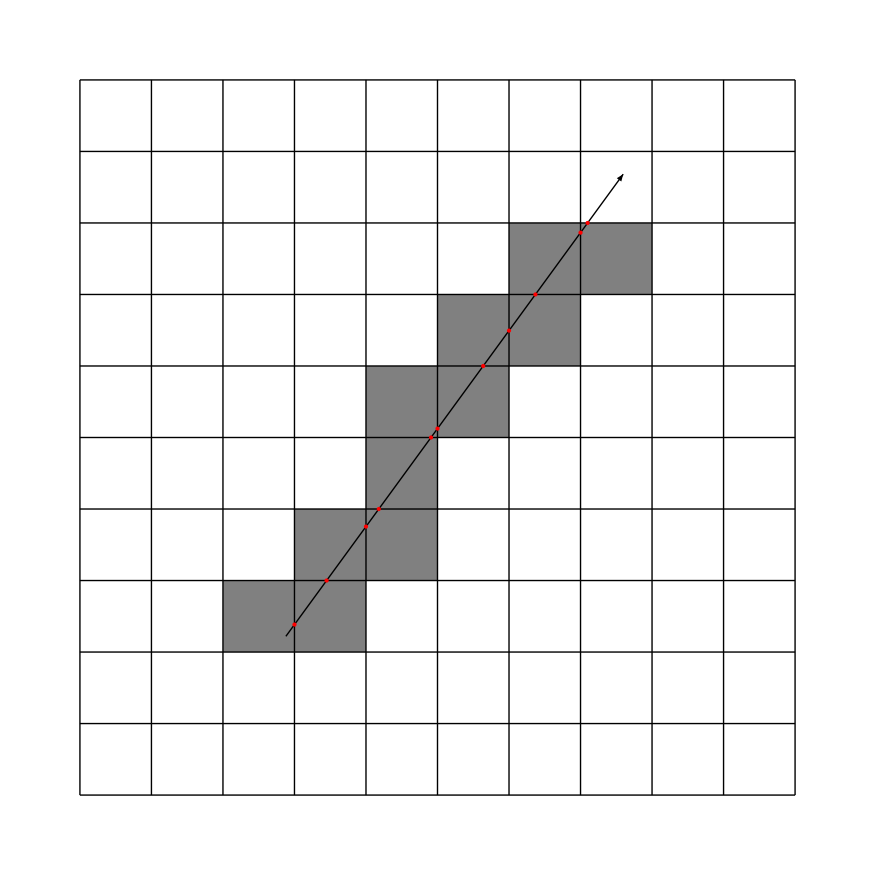

```mathematica
lines={};
fieldHeight=5;
fieldWidth=5;
For[y=-fieldHeight,y<=fieldHeight, ++y,
AppendTo[lines,Line[{{-fieldWidth,y},{fieldWidth,y}}]]
]
For[x=-fieldWidth,x<=fieldWidth,++x,
AppendTo[lines,Line[{{x,-fieldHeight},{x,fieldHeight}}]]
]
startPoint={-2.12,-2.78};
dir=Normalize[{1,1.37}];
currentCell=Floor[startPoint];
step={1,1};
rects={Rectangle[currentCell,currentCell+1]};
deltaStep=1/dir;
tmax=((currentCell+1)-startPoint)/dir;
currentT=0;
intersectionTs={Min[tmax[[1]],tmax[[2]]]};
Do[
If[tmax[[1]]<tmax[[2]],
tmax[[1]]+=deltaStep[[1]];
currentCell[[1]]+=1;
,
tmax[[2]]+=deltaStep[[2]];
currentCell[[2]]+=1;
];
AppendTo[intersectionTs,Min[tmax[[1]],tmax[[2]]]];
AppendTo[rects,Rectangle[currentCell,currentCell+1]];
,10]
intersectionPoints={};
For[i=0,i<Length[intersectionTs],++i,
t=intersectionTs[[i+1]];
AppendTo[intersectionPoints,Point[{startPoint[[1]]+dir[[1]]*t,startPoint[[2]]+dir[[2]]*t}]]
]
intersectionTs
Graphics[{Point[startPoint],Gray,rects,Black,Arrow[{startPoint,startPoint+dir*8}],lines,Red,intersectionPoints}]
```

```mathematica
lines={};
numCells={16,9}
X[vec_]:=vec[[1]];
Y[vec_]:=vec[[2]];
Z[vec_]:=vec[[3]];
cellSize={1,1};
maxDepth=8;
For[y=0,y<=Y[numCells], ++y,
AppendTo[lines,Polygon[{{X[numCells]*X[cellSize],y*Y[cellSize],0},{0,y*Y[cellSize], 0},{0,y*Y[cellSize],maxDepth},{X[numCells]*X[cellSize],y*Y[cellSize], maxDepth}}]]
]
For[x=0,x≤X[numCells], ++x,
AppendTo[lines,Polygon[{{x*X[cellSize],Y[numCells]*Y[cellSize],0},{x*X[cellSize],0, 0},{x*X[cellSize],0, maxDepth},{x*X[cellSize],Y[numCells]*Y[cellSize],maxDepth}}]]
]

depthBuffer=Table[Table[(Sin[x*0.5]*0.5+0.5)*(Sin[y]*0.5+0.5)*0.75,{y,1,Y[numCells]}],{x,1,X[numCells]}];
depthPlanes={};
For[y=0,y<Y[numCells],++y,
For[x=0,x<X[numCells],++x,
depth=depthBuffer[[x+1,y+1]];
plane=Polygon[{{x*X[cellSize],y*Y[cellSize],depth*maxDepth},{(x+1)*X[cellSize],y*Y[cellSize],depth*maxDepth},{(x+1)*X[cellSize],(y+1)*Y[cellSize],depth*maxDepth},{x*X[cellSize],(y+1)*Y[cellSize],depth*maxDepth}}];
AppendTo[depthPlanes,plane];
]
]
rayOrigin={0.3782,0.5175,0.147};
rayDir=Normalize[{1,1,1}];
ToVisualizeSpace[vec_]:={X[vec],1-Y[vec],1-Z[vec]}*{X[numCells]*X[cellSize],Y[numCells]*Y[cellSize],maxDepth};
rayArrow=Arrow[{ToVisualizeSpace[rayOrigin],ToVisualizeSpace[rayOrigin+rayDir*0.3]}];
Graphics3D[{Opacity[0.0125],lines,Opacity[1],depthPlanes,rayArrow}]
```

{16,9}

-Graphics3D-

```mathematica
1280/720
```

16/9